```mathematica
Quit
```

```mathematica
$MachineName
```

eos01

```mathematica
Directory[]
```

/home/ashmat

```mathematica
SetDirectory["/home/ashmat/Projects/myxo-project/"];
```

```mathematica
Get["BiharmonicSolverFourier.wl"]
```

```mathematica
params={S0->1,l->1,lM->7.0/3,lm->0.7/3};
W=10;
S[r_]:=S0 f[r/l]
f[x_]:=x √((0.34+0.07 x^2)/(1+0.41 x^2+0.07 x^4))
θ[ϕ_]:=ϕ/2
Q[x_,y_]:={{S[r] Cos[2θ[ϕ]],S[r] Sin[2θ[ϕ]]},{S[r] Sin[2θ[ϕ]],-S[r] Cos[2θ[ϕ]]}}/.{r->√(x^2+y^2),ϕ->ArcTan[x,y]}
```

```mathematica
A[x_,y_]:=1/2(IdentityMatrix[2]+Q[x,y])
Σ[x_,y_]:=1/2 IdentityMatrix[2](lM^2+lm^2)+1/2 Q[x,y](lM^2-lm^2)
G[x1_,y1_,x2_,y2_]:=1/2(A[x1,y1]PDF[MultinormalDistribution[{x1,y1},Σ[x1,y1]],{x2,y2}]
+A[x2,y2]PDF[MultinormalDistribution[{x2,y2},Σ[x2,y2]],{x1,y1}])
```

```mathematica
cfG=Compile[{x1,y1,x2,y2},G[x1,y1,x2,y2]/.params//Evaluate];
```

```mathematica
LaunchKernels[2$ProcessorCount];(*start parallel kernels if not already running*)
```

LinkObject::linkd: Unable to communicate with closed link LinkObject[/usr/local/math/math1410/Executables/wolfram -noinit -subkernel -wstp,709,134].

LinkObject::linkd: Unable to communicate with closed link LinkObject[/usr/local/math/math1410/Executables/wolfram -noinit -subkernel -wstp,710,135].

LinkObject::linkd: Unable to communicate with closed link LinkObject[/usr/local/math/math1410/Executables/wolfram -noinit -subkernel -wstp,711,136].

General::stop: Further output of LinkObject::linkd will be suppressed during this calculation.

Parallel`Developer`ConnectKernel::failinit: 47 of 144 kernels failed to initialize.

```mathematica
sol2=solveBiharmonicFourier[cfG,200,100,"Method"->"Compiled"];
```

===============================================

Biharmonic Fourier Solver

===============================================

Grid size: 200^4 = 1600000000 points

Domain: [-100, 100]^2 x [-100, 100]^2

Method: Compiled

-----------------------------------------------

[Step 1/4] Evaluating G_{ij} on 4D grid (parallelized)...

Extracting G components...

Done. (198.76 s)

Memory for G components: ~48828.1 MB

[Step 2/4] Computing 4D FFT of G components...

Done. (69.47 s)

[Step 3/4] Pointwise division in Fourier space...

Regularization eps = π^4/160000000000000000

Done. (152.77 s)

[Step 4/4] Computing inverse 4D FFT...

Done. (16.46 s)

-----------------------------------------------

Max |f| = 4.47×10^-1

Solution complete.

===============================================

```mathematica
sol=Association[];
sol["fdiag"]=Developer`FromPackedArray[Import["/scratch/ashot/solution.h5",{"Datasets","/fdiag"}]];
sol["grid"]=Developer`FromPackedArray[Import["/scratch/ashot/solution.h5",{"Datasets","/grid"}]];
sol["n"]=Length[sol["grid"]];
Import["/scratch/ashot/solution.h5","Dimensions"]
```

<|/f→{400,400,400,400},/fdiag→{400,400},/grid→{400}|>

```mathematica
fdiag=ListInterpolation[sol["fdiag"],{sol["grid"],sol["grid"]},InterpolationOrder->2];
```

```mathematica
defect[x_,y_]:=Block[{φ=ArcTan[x,y],θ},θ=φ/2;Sign[y]{Cos[θ],Sin[θ],0}];
With[{W=30,Z=0.3},Show[
Plot3D[fdiag[x,y],{x,-W,W},{y,-W,W},PlotPoints->100,PlotRange->All,MaxRecursion->2],
StreamPlot3D[defect[x,y],{x,-W,W},{y,-W,W},{z,Z-0.1,Z+0.1},StreamScale->None,
RegionFunction->Function[{x,y,z,vx,vy,vz},x^2+y^2<=W^2],RegionBoundaryStyle->None,
StreamColorFunction->None,StreamPoints->Table[{r,0,Z},{r,-W,0,3}]],
PlotRange->All,
AxesLabel->{"x","y","Var[p]"},
PlotLabel->"Pressure fluctuations"
]
]
```

-Graphics3D-

```mathematica
Mod[π+ArcTan[-1,0.01],2π]-π
```

3.13159

```mathematica
defect[-1,-0.01]
```

{0.00499981,-0.999988}

```mathematica
reg=Cylinder[{{0,0,-0.1},{0,0,0.1}},W];
```

```mathematica
With[{W=30},StreamPlot3D[defect[x,y],{x,-W,W},{y,-W,W},{z,-0.1,0.1},StreamScale->None,
RegionFunction->Function[{x,y,z,vx,vy,vz},x^2+y^2<=W^2],RegionBoundaryStyle->None,
StreamColorFunction->None,StreamPoints->Table[{r,0,0},{r,-W,0,3}]]]
```

-Graphics3D-

```mathematica
StreamPlot3D[]
```

```mathematica
sol["n"]
```

400

```mathematica
SliceVectorPlot3D
```

```mathematica
{zMin,zMax}=MinMax[Import["/scratch/ashot/solution.h5","/f","TakeElements"->{200;;200,200;;200,;;,;;}]];
levels=Subdivide[zMin,zMax,11]//Most//Rest
```

{0.0000515394,0.0276551,0.0552587,0.0828622,0.110466,0.138069,0.165673,0.193277,0.22088,0.248484}

```mathematica
getslice[x_,y_]:=Block[{xi,yi},
xi=First@Nearest[sol["grid"]->"Index",x];
yi=First@Nearest[sol["grid"]->"Index",y];
ListInterpolation[Import["/scratch/ashot/solution.h5","/f","TakeElements"->{xi;;xi,yi;;yi,;;,;;}][[1,1]],{sol["grid"],sol["grid"]},InterpolationOrder->2]
]
```

```mathematica
fslice=getslice[0,0];
With[{W=50},Plot3D[fslice[x,y],{x,-W,W},{y,-W,W},PlotPoints->100,PlotRange->All,MaxRecursion->2]]
```

-Graphics3D-

```mathematica
frames=ParallelTable[Block[{fslice},
fslice=getslice[x0,0];
With[{W=20},ContourPlot[fslice[x,y],{x,-W,W},{y,-W,W},Contours->levels,PlotRange->All,PlotLegends->Automatic]]],
{x0,-10,10,0.2}];
```

```mathematica
ListAnimate[frames]
```

```mathematica
Manipulate[Plot[fslice[r Cos[φ],r Sin[φ]],{φ,0,2π}],{r,1,Max[sol["grid"]]}]
```

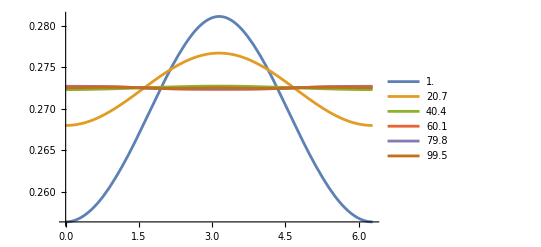

```mathematica
With[{rs=Subdivide[1,Max[sol["grid"]],5]},Plot[Table[fdiag[r Cos[φ],r Sin[φ]],{r,rs}]//Evaluate,{φ,0,2π}, PlotLegends->rs,PlotRange->All]]
```

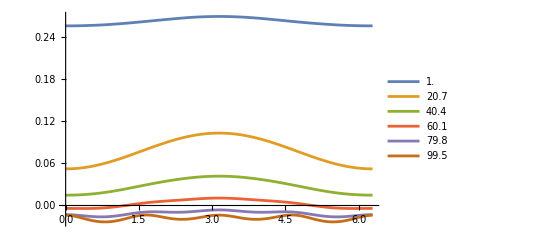

```mathematica
fslice=getslice[0,0];
With[{rs=Subdivide[1,Max[sol["grid"]],5]},Plot[Table[fslice[r Cos[φ],r Sin[φ]],{r,rs}]//Evaluate,{φ,0,2π}, PlotLegends->rs,PlotRange->All]]
```

```mathematica
f[1,2]
```

0.251047

```mathematica
Import["/scratch/ashot/solution.h5","Datasets"]
```

{/f,/fdiag,/grid}

```mathematica
Import["/scratch/ashot/solution.h5","Dimensions"]
```

<|/f→{400,400,400,400},/fdiag→{400,400},/grid→{400}|>

```mathematica
values[sol_]:=Block[{fdiag,vals,maxval,n=Length[sol["grid"]]},
fdiag=sol["fdiag"];
vals=Flatten[Table[{sol["grid"][[i]],sol["grid"][[j]],fdiag[[i,j]]},{i,n},{j,n}],1];
maxval=Max[vals[[;;,3]]];
vals[[;;,3]]=vals[[;;,3]]-maxval;
vals
];
```

```mathematica
values[sol]
```

```mathematica
ListPlot3D[sol["fdiag"],Mesh->Full]
```

-Graphics3D-

```mathematica
With[{W=30},ListPlot3D[values[sol],PlotRange->{{-W,W},{-W,W}},PlotLabel->"f(r, r)", Mesh->Full]]
```

-Graphics3D-

```mathematica
sols[{32,8.0}]=solveBiharmonicFourier[cfG,32,8.0,"Method"->"Compiled"];
sols[{64,16.0}]=solveBiharmonicFourier[cfG,64,16.0,"Method"->"Compiled"];
sols[{128,32.0}]=solveBiharmonicFourier[cfG,128,32.0,"Method"->"Compiled"];
```

═══════════════════════════════════════════════

Biharmonic Fourier Solver

═══════════════════════════════════════════════

Grid size: 32^4 = 1048576 points

Domain: [-8., 8.]^2 x [-8., 8.]^2

Method: Compiled

───────────────────────────────────────────────

[Step 1/4] Evaluating G_{ij} on 4D grid (parallelized)...

Extracting G components...

Done. (0.4 s)

Memory for G components: ~32. MB

[Step 2/4] Computing 4D FFT of G components (4 parallel FFTs)...

Done. (0.18 s)

[Step 3/4] Pointwise division in Fourier space...

Regularization eps = 2.27×10^-8

Done. (0.21 s)

[Step 4/4] Computing inverse 4D FFT...

Done. (0.01 s)

───────────────────────────────────────────────

Max |f| = 1.415

Solution complete.

═══════════════════════════════════════════════

═══════════════════════════════════════════════

Biharmonic Fourier Solver

═══════════════════════════════════════════════

Grid size: 64^4 = 16777216 points

Domain: [-16., 16.]^2 x [-16., 16.]^2

Method: Compiled

───────────────────────────────────────────────

[Step 1/4] Evaluating G_{ij} on 4D grid (parallelized)...

Extracting G components...

Done. (1.79 s)

Memory for G components: ~512. MB

[Step 2/4] Computing 4D FFT of G components (4 parallel FFTs)...

Done. (1.7 s)

[Step 3/4] Pointwise division in Fourier space...

Regularization eps = 8.86×10^-11

Done. (1.97 s)

[Step 4/4] Computing inverse 4D FFT...

Done. (0.17 s)

───────────────────────────────────────────────

Max |f| = 2.099

Solution complete.

═══════════════════════════════════════════════

═══════════════════════════════════════════════

Biharmonic Fourier Solver

═══════════════════════════════════════════════

Grid size: 128^4 = 268435456 points

Domain: [-32., 32.]^2 x [-32., 32.]^2

Method: Compiled

───────────────────────────────────────────────

[Step 1/4] Evaluating G_{ij} on 4D grid (parallelized)...

Extracting G components...

Done. (25.04 s)

Memory for G components: ~8192. MB

[Step 2/4] Computing 4D FFT of G components (4 parallel FFTs)...

Done. (25.06 s)

[Step 3/4] Pointwise division in Fourier space...

Regularization eps = 3.46×10^-13

Done. (30.75 s)

[Step 4/4] Computing inverse 4D FFT...

Done. (4.17 s)

───────────────────────────────────────────────

Max |f| = 2.791

Solution complete.

═══════════════════════════════════════════════

```mathematica
With[{n=300},4*n^4*8/1024.^3]
```

241.399

```mathematica
values[sol_]:=Module[{vals,maxval,grid,fs},
grid=sol["grid"];fs=sol["f"];
vals=Flatten[Table[{grid[[i]],grid[[j]],sol["f"][[i,j,i,j]]},{i,sol["n"]},{j,sol["n"]}],1];
maxval=Max[vals[[;;,3]]];
vals[[;;,3]]=vals[[;;,3]]-maxval;
vals
];
```

```mathematica
With[{W=32},ListPlot3D[values[sols[{128,32.0}]],PlotRange->{{-W,W},{-W,W}},PlotLabel->"f(r, r)"]]
```

-Graphics3D-

```mathematica
4*n^4*8/1024.^2
```

```mathematica
ListPlot3D[Table[values[sols[k]],{k,Keys[sols]}],PlotRange->{{-W,W},{-W,W}},PlotLabel->"f(r, r)"]
```

-Graphics3D-

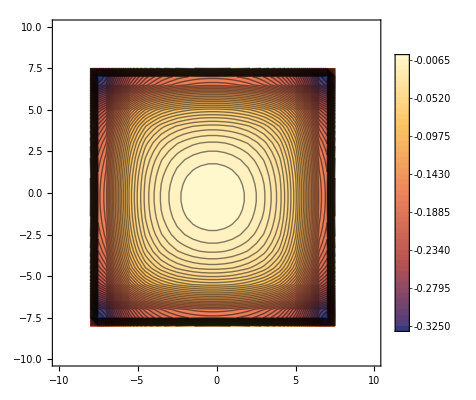
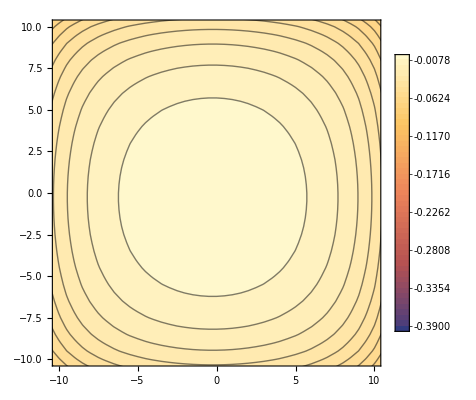
{-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[ListContourPlot[values[sols[k]], Contours->50,PlotLegends->Automatic,PlotRange->{{-W,W},{-W,W}}],{k,Keys[sols]}]
```

```mathematica
Clear[slice]
slice[sol_,x2_?NumericQ,y2_?NumericQ]:=Module[{vals,grid,n,i2,j2, fs},
grid=sol["grid"];fs=sol["f"];
(*Find nearest grid indices*)
i2=Nearest[grid->"Index",x2][[1]];
j2=Nearest[grid->"Index",y2][[1]];
vals=Flatten[Table[{grid[[i]],grid[[j]],fs[[i,j,i2,j2]]},{i,sol["n"]},{j,sol["n"]}],1];
vals[[;;,3]]=vals[[;;,3]] - Max[vals[[;;,3]]];
vals
]
u[r_]:=-1/2 A σ^2 (EulerGamma+Gamma[0,r^2/(2 σ^2)]+Log[r^2/(2 σ^2)])
```

```mathematica
sliceAnalitic=Table[{p[[1]],p[[2]],u[√(p[[1]]^2+p[[2]]^2)]/.{A->1, σ->1}},{p,slice[sols[{128,32.0}],0,0]}];
sliceNumeric=slice[sols[{128,32.0}],0,0];
```

General::munfl: Exp[-1030.93] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1015.04] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-999.4] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

```mathematica
diff={sliceAnalitic[[;;,1]],sliceAnalitic[[;;,2]],sliceAnalitic[[;;,3]]-sliceNumeric[[;;,3]]}ᵀ
```

```mathematica
Plot3D[u[√(x^2+y^2)]/.{A->1, σ->1},{x,-W,W},{y,-W,W}]
```

-Graphics3D-

```mathematica
ListPlot3D[diff,PlotRange->{{-W,W},{-W,W}, All},PlotLabel->"f(r, 0)"]
```

-Graphics3D-

```mathematica
ListPlot3D[{sliceAnalitic-sliceNumeric},PlotRange->{{-W,W},{-W,W}, All},PlotLabel->"f(r, 0)"]
```

-Graphics3D-

```mathematica
Show[
ListPlot3D[slice[sols[{128,32.0}],0,0],PlotRange->{{-W,W},{-W,W}, All},PlotLabel->"f(r, 0)"],
Plot3D[u[√(x^2+y^2)]/.{A->1, σ->1},{x,-W,W},{y,-W,W}]
]
```

-Graphics3D-

```mathematica
Manipulate[
ListPlot3D[slice[sols[{128,32.0}],x0,y0],PlotRange->{{-W,W},{-W,W}, All},PlotLabel->"f(r, 0)"],
{{x0,0},-W,W},{{y0,0},-W,W}]
```